Options and Functions

```mathematica
SetOptions[ListLinePlot, ImageSize->800, Frame -> True, Axes->False];

PrepareData[filename_] := Block[{data, mapping, dataTmp, dataKugelkoordinaten},
data = Drop[Import["/home/nils/Projects/C/Handschuh/USB/driver/gesture_data/" <> filename <> ".dat", "Table"], -1];
mapping = CoordinateTransformData["Cartesian"->"Spherical", "Mapping"];
(* r, θ, ϕ *)
Quiet[data /. {x_,y_,z_} -> mapping[{z,x,y}]]
]
PlotCalibrate[data_] := ListLinePlot[{data[[All, 1,1]], data[[All, 1,2]], data[[All, 1,3]]}, PlotRange->Full, PlotLegends->{"r","θ","ϕ"}]
PlotData[data_] := ListLinePlot[{data[[All, 1]], data[[All, 2]], data[[All, 3]]}, PlotRange->{Full, {-3,3}}, PlotLegends->{"r","θ","ϕ"}]
Calibrate[data_, span_] := Block[{dataGood = data/.{x_,y_,Indeterminate} -> {x,y,0}}, # - {0}~Join~Mean[dataGood[[span]]][[{2,3}]]&/@dataGood]
ClassifyManual[data_, spanlist_, class_] := # -> class&/@ Flatten[data[[#]]&/@spanlist,1]
WordReplacement = {"Steady" -> 0, "Down" -> -1,"Up" -> 1, "Right" -> 2};
PlotClassify[data_, classfifier_] := Show[{PlotData[data], ListLinePlot[classfifier[data] /. WordReplacement, PlotRange->Full, PlotStyle->Black]}]
```

Data

```mathematica
(* Gesture Down *)
dataGestureDown = PrepareData["gesture_down"];
dataGestureDown = Calibrate[dataGestureDown, 2;;400];
dataGestureDown2 =  PrepareData["gesture_down2"];
dataGestureDown = dataGestureDown ~Join~ Calibrate[dataGestureDown2, 2;;300];
(* Gesture Up *)
dataGestureUp = PrepareData["gesture_up"];
dataGestureUp = Calibrate[dataGestureUp, 2;;700];
(* Gesture Right *)
dataGestureRight = PrepareData["gesture_right"];
dataGestureRight = Calibrate[dataGestureRight, 2;;400];

(* Poses *)
dataPoseSteady = ClassifyManual[dataGestureDown, {2;;400,1100;;1700}, "Steady"];
dataPoseDown = ClassifyManual[dataGestureDown,{ 500;;950,1850;;1950,2300;;2500}, "Down"];
dataPoseUp = ClassifyManual[dataGestureUp,{ 900;;1100,1550;;1700,2550;;2650}, "Up"];
dataPoseRight = ClassifyManual[dataGestureRight,{ 1000;;1200,1750;;1900,2250;;2300}, "Right"];

(* Classifier *)
classified = Classify[dataPoseSteady ~Join~ dataPoseDown~Join~dataPoseUp~Join~dataPoseRight];
```

## Test

Data

```mathematica
(* Gesture Down Test *)
dataGestureDownTest =  PrepareData["gesture_down_test"];
dataGestureDownTest = Calibrate[dataGestureDownTest, 2;;700];
(* Gesture Up Test *)
dataGestureUpTest =  PrepareData["gesture_up_test"];
dataGestureUpTest = Calibrate[dataGestureUpTest, 2;;200];
```

Plots

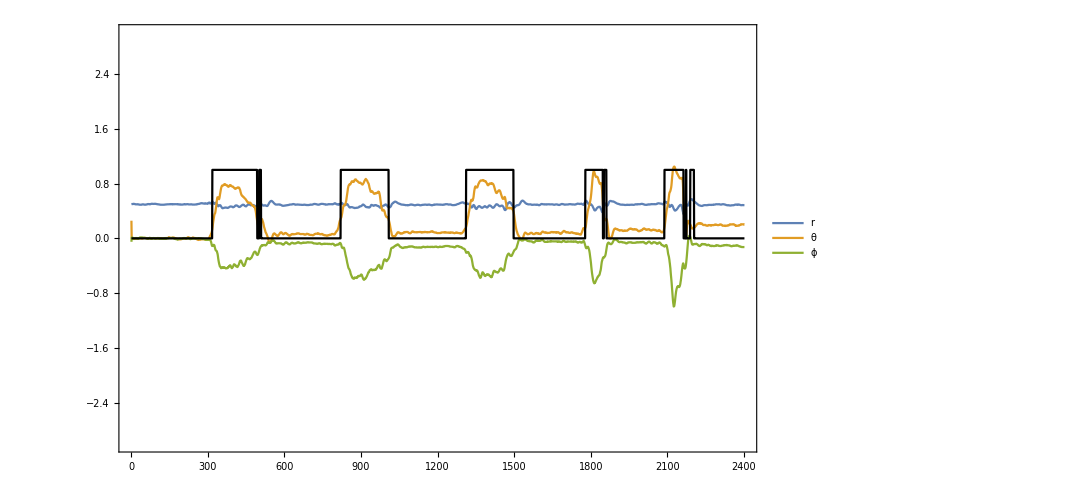

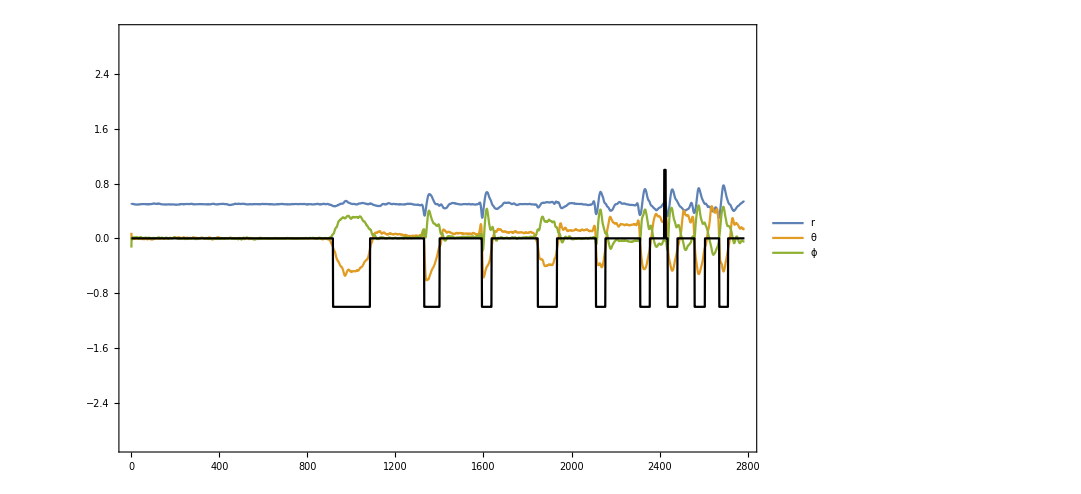

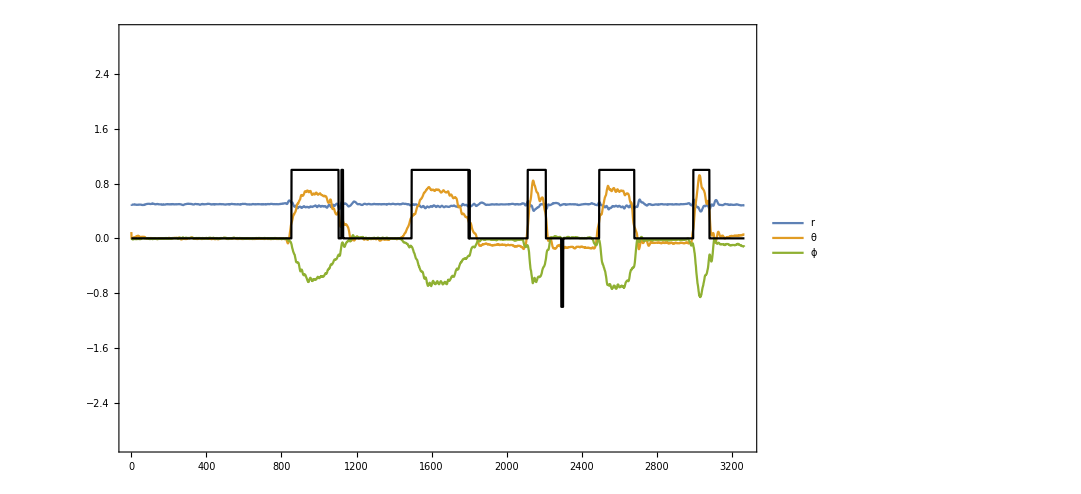

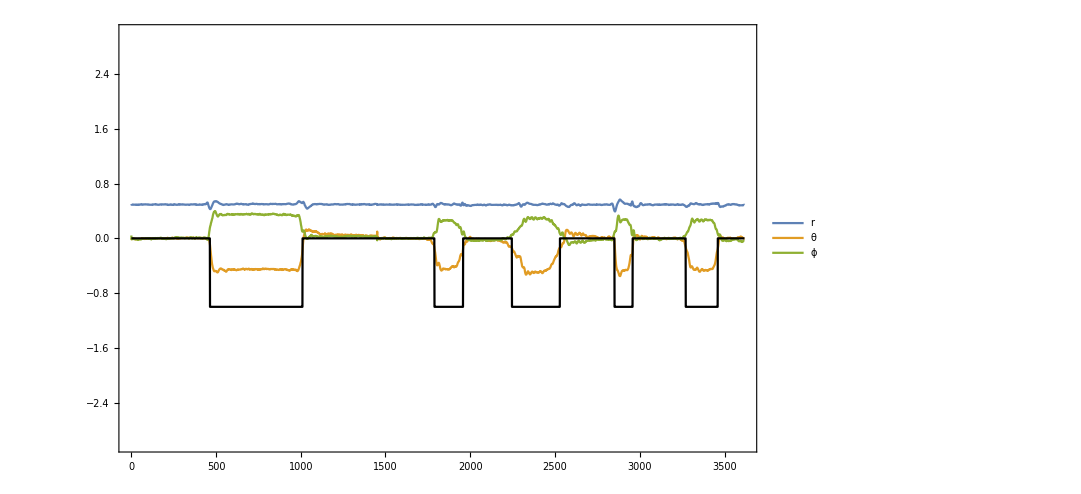

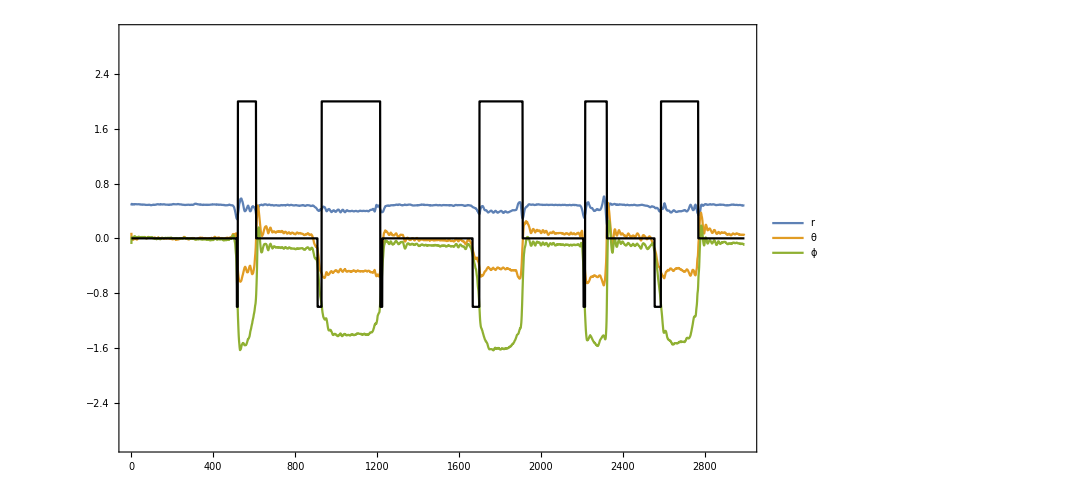

```mathematica
PlotClassify[dataGestureUpTest, classified]
PlotClassify[dataGestureDownTest, classified]
PlotClassify[dataGestureUp, classified]
PlotClassify[dataGestureDown, classified]
PlotClassify[dataGestureRight, classified]
```